```mathematica
<<MaTeX`
SetOptions[MaTeX,"Preamble"->{"\\usepackage{mathtext}" ,
"\\usepackage[T2A]{fontenc}",
"\\usepackage[utf8]{inputenc}",
"\\usepackage[english,russian]{babel}",
"\\usepackage{units}"}];
```

```mathematica
files=FileNames["*.csv",NotebookDirectory[]]
```

{/Users/yaroslav/mipt/bachelor-3/semester-2/laboratory/11.1/data.csv}

```mathematica
importfile = files⟦1⟧
```

/Users/yaroslav/mipt/bachelor-3/semester-2/laboratory/11.1/data.csv

```mathematica
raw = Import[importfile];
```

```mathematica
makeAssoc[header_][row_]:=<|header->row//Thread|>;
makeDataset@raw_:=With[{header=raw⟦1⟧,data=raw⟦2;;⟧},
makeAssoc@header/@data
]//Dataset;
```

```mathematica
rawᵀ
```

```mathematica
raw={{"u",0,0.41,0.82,1.23,1.64,2.05,2.46,2.87},{"ut",0,10,20,30,40,50,60,70},{"prov",0.093,0.095,0.098,0.106,0.118,0.109,0.111,0.115},{"proverr",0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001},{"pp",0.73,0.43,0.27,0.18,0.106,0.097,0.064,0.048},{"pperr",0.01,0.01,0.01,0.01,0.001,0.001,0.001,0.001}}ᵀ
```

{{u,ut,prov,proverr,pp,pperr},{0,0,0.093,0.001,0.73,0.01},{0.41,10,0.095,0.001,0.43,0.01},{0.82,20,0.098,0.001,0.27,0.01},{1.23,30,0.106,0.001,0.18,0.01},{1.64,40,0.118,0.001,0.106,0.001},{2.05,50,0.109,0.001,0.097,0.001},{2.46,60,0.111,0.001,0.064,0.001},{2.87,70,0.115,0.001,0.048,0.001}}

```mathematica
raw={{"a","n"},{0,653},{10,609},{20,556},{30,525},{40,467},{50,413},{60,367},{70,331},{80,298},{90,268},{103,236}}
```

{{a,n},{0,653},{10,609},{20,556},{30,525},{40,467},{50,413},{60,367},{70,331},{80,298},{90,268},{103,236}}

```mathematica
dataset=makeDataset[raw]
```

```mathematica
datasetWithErrors=dataset[All,<|"u"->(Around[#u,0.01]&),"t"->(10^3 Around[#u,0.01]/Around[41,1]&),"ut"->(Around[#ut,1]&),"prov"->(Around[#prov,#proverr+Around[0.015,0.02(2/(#prov)-1)]]&),"pp"->(Around[#pp,#pperr+Around[0.015,0.02(2/(#pp)-1)]]&)|>]
```

```mathematica
datasetWithErrors//Normal
```

```mathematica
datasetWithErrors=Dataset[{<|"u"->0,"t"->0,"ut"->0.01.0,"prov"->0.0930.016,"pp"->0.7300.025|>,<|"u"->0.4100.010,"t"->10.000.34,"ut"->10.01.0,"prov"->0.0950.016,"pp"->0.4300.025|>,<|"u"->0.8200.010,"t"->20.00.5,"ut"->20.01.0,"prov"->0.0980.016,"pp"->0.2700.025|>,<|"u"->1.2300.010,"t"->30.00.8,"ut"->30.01.0,"prov"->0.1060.016,"pp"->0.1800.025|>,<|"u"->1.6400.010,"t"->40.01.0,"ut"->40.01.0,"prov"->0.1180.016,"pp"->0.1060.016|>,<|"u"->2.0500.010,"t"->50.01.2,"ut"->50.01.0,"prov"->0.1090.016,"pp"->0.0970.016|>,<|"u"->2.4600.010,"t"->60.01.5,"ut"->60.01.0,"prov"->0.1110.016,"pp"->0.0640.016|>,<|"u"->2.8700.010,"t"->70.01.7,"ut"->70.01.0,"prov"->0.1150.016,"pp"->0.0480.016|>}]
```

```mathematica
dataset1=datasetWithErrors[All,<|"u"->(#u&),"t"->(Around[24,1]+#t&),"prov"->(#prov&),"pp"->(#pp&),"tinv"->(1/(273.16+Around[24,1]+#t)&),"spr"->(Around[13.4 ,0.1]/(#prov  π (Around[0.07,0.01] )^2)&),"lnspr"->(Log[Around[13.4 ,0.1]/(#prov  π (Around[0.07,0.01] )^2 Around[13.4 ,0.1]/(dataset[1,"prov"]  π (Around[0.07,0.01])^2))]&),"spp"->(Around[39.2,0.1]/(#pp Around[4.1,0.1]^2 10^3)&),"lnspp"->(Log[Around[39.2,0.1]/(#pp Around[4.1,0.1]^2 10^3 Around[39.2,0.1]/(dataset[1,"pp"] Around[4.1,0.1]^2 10^3))]&)|>]
```

```mathematica
dataset1[1,"lnspr"]
```

Around[2.2204460492503128*^-16, 0.17204301075268816]

```mathematica
dataset3=dataset1[All,<|"u"->(hiTeXForm[#u]&),"t"->(hiTeXForm[#t]&),"prov"->(hiTeXForm[#prov]&),"pp"->(hiTeXForm[#pp]&),"tinv"->(hiTeXForm[10^3#tinv]&),"spr"->(hiTeXForm[10^-3#spr]&),"lnspr"->(hiTeXForm[#lnspr]&),"spp"->(hiTeXForm[10^3#spp]&),"lnspp"->(hiTeXForm[#lnspp]&)|>]
```

```mathematica
dataset1//Normal
```

```mathematica
dataset1=Dataset[{<|"u"->0,"t"->24.01.0,"prov"->0.0930.016,"pp"->0.7300.025,"tinv"->0.0033650.000011,"spr"->9.43.110^3,"lnspr"->0.,"spp"->0.003190.00019,"lnspp"->0|>,<|"u"->0.4100.010,"t"->34.01.1,"prov"->0.0950.016,"pp"->0.4300.025,"tinv"->0.0032560.000011,"spr"->9.23.010^3,"lnspr"->0.00.4,"spp"->0.00540.0004,"lnspp"->0.530.09|>,<|"u"->0.8200.010,"t"->44.01.1,"prov"->0.0980.016,"pp"->0.2700.025,"tinv"->0.0031530.000011,"spr"->8.92.910^3,"lnspr"->0.00.4,"spp"->0.00860.0009,"lnspp"->0.990.12|>,<|"u"->1.2300.010,"t"->54.01.3,"prov"->0.1060.016,"pp"->0.1800.025,"tinv"->0.0030570.000012,"spr"->8.22.710^3,"lnspr"->-0.10.4,"spp"->0.01300.0019,"lnspp"->1.400.16|>,<|"u"->1.6400.010,"t"->64.01.4,"prov"->0.1180.016,"pp"->0.1060.016,"tinv"->0.0029660.000012,"spr"->7.42.310^3,"lnspr"->-0.20.4,"spp"->0.02200.0035,"lnspp"->1.930.17|>,<|"u"->2.0500.010,"t"->74.01.6,"prov"->0.1090.016,"pp"->0.0970.016,"tinv"->0.0028810.000013,"spr"->8.02.610^3,"lnspr"->-0.20.4,"spp"->0.0240.004,"lnspp"->2.020.18|>,<|"u"->2.4600.010,"t"->84.01.8,"prov"->0.1110.016,"pp"->0.0640.016,"tinv"->0.0028000.000014,"spr"->7.82.510^3,"lnspr"->-0.20.4,"spp"->0.0360.009,"lnspp"->2.430.26|>,<|"u"->2.8700.010,"t"->94.02.0,"prov"->0.1150.016,"pp"->0.0480.016,"tinv"->0.0027240.000015,"spr"->7.62.410^3,"lnspr"->-0.20.4,"spp"->0.0490.016,"lnspp"->2.720.34|>}]
```

```mathematica
"0.000(14)"
```

```mathematica
dataset3=dataset1[All,<|"t"->(hiTeXFormVal[#t]&),"tinv"->(hiTeXFormVal[10^3#tinv]&),"spr"->(hiTeXFormVal[10^-3#spr]&),"lnspr"->(hiTeXForm[#lnspr]&),"spp"->(hiTeXForm[10^3#spp]&),"lnspp"->(hiTeXForm[#lnspp]&)|>]
```

```mathematica
dataset2=dataset1[All,<|"tinv"->(1/(24+#t)&),"lnspp"->(#lnspp&)|>]
```

```mathematica
MantErr[a_]:=If[10≤Round[FromDigits[RealDigits[a["Uncertainty"]]⟦1,;;3⟧],10]/10≤19,Round[FromDigits[RealDigits[a["Uncertainty"]]⟦1,;;3⟧],10]/10,Round[FromDigits[RealDigits[a["Uncertainty"]]⟦1,;;2⟧],10]/10]
MantExp[a_]:=If[10≤Round[FromDigits[RealDigits[a["Uncertainty"]]⟦1,;;3⟧],10]/10≤19,MantissaExponent[a["Uncertainty"]]⟦2⟧-2,MantissaExponent[a["Uncertainty"]]⟦2⟧-1]
DigVal[a_]:=If[RealAbs[a["Value"]/10^MantExp[a]]<.01,MantissaExponent[MantErr[a]]⟦2⟧,MantissaExponent[a["Value"]]⟦2⟧-MantExp[a]+1]
MantVal[a_]:=If[RealAbs[a["Value"]/10^MantExp[a]]<.01,0,Sign[a["Value"]]Round[FromDigits[RealDigits[a["Value"]]⟦1,;;DigVal[a]⟧],10]/10]
hiTeXForm[x_]:=Which[Head[x]===Real||Head[x]===Integer,IntegerPart[x],-3≤MantExp[x]≤-1,ToString[Row[{PaddedForm[MantVal[x]*10.^MantExp[x],{DigVal[x],Abs[MantExp[x]]},NumberPadding->{"","0"}],"(",MantErr[x],")"}]],MantExp[x]==0,ToString[Row[{MantVal[x],"(",MantErr[x],")"}]],True,ToString[Row[{MantVal[x],"(",MantErr[x],")e",MantExp[x]}]]]
hiTeXFormVal[x_]:=Which[Head[x]===Real,IntegerPart[x],MantExp[x]≠0,ToString[PaddedForm[x["Value"],{DigVal[x],Abs[MantExp[x]]},NumberPadding->{"","0"}]],MantExp[x]==0,MantVal[x]]
hiTeXFormErr[x_]:=Which[Head[x]===Real,IntegerPart[x],MantExp[x]≠0,ToString[PaddedForm[MantErr[x]*10.^MantExp[x],{DigVal[x],Abs[MantExp[x]]},NumberPadding->{"","0"}]],MantExp[x]==0,MantErr[x]]
```

```mathematica
dataset3=dataset[All,<|"ut"->(hiTeXForm[#ut]&),"prov"->(hiTeXForm[#prov]&)|>]
```

Failure[…]

```mathematica
dataset4=dataset1[All,<|"TexpAbs"->(hiTeXFormVal[#T]&),"TexpErr"->(hiTeXFormErr[#T]&),"WexpAbs"->(hiTeXFormVal[#W]&),"WexpErr"->(hiTeXFormErr[#W]&)|>]
```

```mathematica
Export[NotebookDirectory[]<>"datasethi.csv",dataset3,"TextDelimiters"->""]
```

/Users/yaroslav/mipt/bachelor-3/semester-2/laboratory/11.1/datasethi.csv

```mathematica
raw={Table[n+RandomInteger[],{n,10}],Table[n,{n,10}]}
```

{{2,2,3,4,6,7,7,8,9,11},{1,2,3,4,5,6,7,8,9,10}}

{{3.36519,0},{3.25563,0.529259},{3.15298,0.994623},{3.05661,1.40009},{2.96595,1.92961},{2.88052,2.01833},{2.79987,2.43416},{2.72361,2.72184}}

{{3.3650.011,0},{3.2560.011,0.530.09},{3.1530.011,0.990.12},{3.0570.012,1.400.16},{2.9660.012,1.930.17},{2.8810.013,2.020.18},{2.8000.014,2.430.26},{2.7240.015,2.720.34}}

FittedModel[14.2229-4.20471 x]

14.20.5

-4.200.15

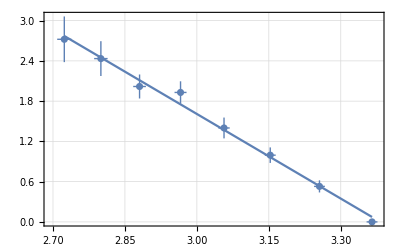

```mathematica
data=Table[{10^3 dataset1[n,"tinv"]["Value"],dataset1[n,"lnspp"]["Value"]},{n,8}];
data={{3.365190469780589,0},{3.255632243781742,0.5292593254548288},{3.152982721654685,0.9946225751440623},{3.0566083873334144,1.4000876832522267},{2.9659508838533633,1.9296054400303697},{2.8805161885009793,2.018333555639054},{2.7998656064508904,2.434161450782765},{2.7236082361913057,2.7218435232345457}}
dataerr=Table[{10^3 dataset1[n,"tinv"],dataset1[n,"lnspp"]},{n,8}]
fit=LinearModelFit[data,{1,x},x](*   f = a + b * x   *)
fit["ParameterTable"];
a=Around[fit["BestFitParameters"]⟦1⟧,fit["ParameterErrors"]⟦1⟧]
b=Around[fit["BestFitParameters"]⟦2⟧,fit["ParameterErrors"]⟦2⟧]
(*fit["BestFitParameters"]⟦1⟧
fit["BestFitParameters"]⟦2⟧*)
(*hiTeXForm[a]
hiTeXForm[b]*)
Show[ListPlot[dataerr,Frame->True,FrameStyle->Black,GridLines->Automatic,LabelStyle->{NumberPoint->","},BaseStyle->{FontFamily->"CMU Serif"},(*PlotLegends->MaTeX@functions,*)FrameLabel->MaTeX@{"10^{-3} \\cdot T^{-1},\\text{ K}^{-1}","\\ln \\left(\\sigma_{\\text{пп}}/\\sigma_{\\text{пп}0} \\right)"}],Plot[fit["BestFitParameters"]⟦1⟧+fit["BestFitParameters"]⟦2⟧x,{x,Min[data⟦All,1⟧],Max[data⟦All,1⟧]}]]
```

```mathematica
data
```

```mathematica
data={{3.365190469780589,0},{3.255632243781742,0.5292593254548288},{3.152982721654685,0.9946225751440623},{3.0566083873334144,1.4000876832522267},{2.9659508838533633,1.9296054400303697},{2.8805161885009793,2.018333555639054},{2.7998656064508904,2.434161450782765},{2.7236082361913057,2.7218435232345457}}
```

```mathematica
dataerr=Table[{dataset1[n,"tinv"],10^3 dataset1[n,"lnspp"]},{n,8}]
```

{{0.0033650.000011,0},{0.0032560.000011,529.90.},{0.0031530.000011,995.116.},{0.0030570.000012,1400.155.},{0.0029660.000012,1930.166.},{0.0028810.000013,2018.179.},{0.0028000.000014,2434.259.},{0.0027240.000015,2722.340.}}

```mathematica
Subscript[t, комн]=25 °
```

```mathematica
Table[10.n 41 /10^3  ,{n,10}]
```

{0.41,0.82,1.23,1.64,2.05,2.46,2.87,3.28,3.69,4.1}

```mathematica
Subscript[U, поправки]=-20 мкВ
```

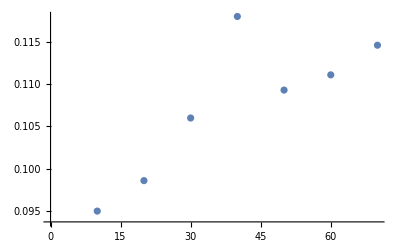

```mathematica
ListPlot[dataset1]
```

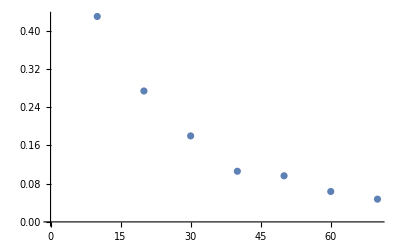

```mathematica
ListPlot[dataset2]
```

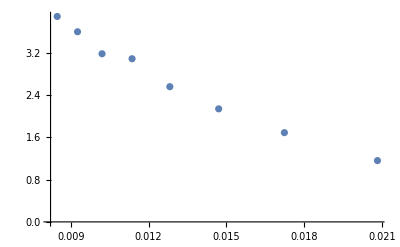

```mathematica
ListPlot[dataset1[All,<|"tinv"->(1/(24+#t)&),"lnspp"->(#lnspp&)|>]]
```

```mathematica
-4.200.15 1000(-2) 1.38 10^-23/1.6 10^19
```

0.7250.027

```mathematica
dataset1[1,"lnspp"]
```

-0.0000326886

```mathematica
PaddedForm[-3.0,3]
```

-3.

```mathematica
RealDigits[-123.55555]
```

{{1,2,3,5,5,5,5,5,0,0,0,0,0,0,0,0},3}

```mathematica
Sign[Around[-3,1]["Value"]]
```

-1

```mathematica
MantErr[Around[111.,1.]]
```

10

```mathematica
Head[Around[0,1]]
```

Around

```mathematica
Head[0]
```

Integer

```mathematica
MantissaExponent[a["Value"]]⟦2⟧-MantExp[a]+1
```

```mathematica
MantissaExponent[Around[0.,1.]["Value"]]
```

{0.,-323}

```mathematica
RealDigits[0.00]
```

{{0},-323}

```mathematica
MantissaExponent[10]
```

{1/10,2}

```mathematica
Around[0,1.]["Value"]===0.
```

True

```mathematica
MantissaExponent[Around[0.,1.]["Uncertainty"]]⟦2⟧
```

1

```mathematica
MantExp[Around[0.00,0.00000175]]
```

-7

```mathematica
MantissaExponent[MantErr[Around[2.2204460492503128*^-16, 0.17204301075268816]]]⟦2⟧
```

2

```mathematica
Around[2.2204460492503128*^-16, 0.17204301075268816]["Value"]===0.
```

```mathematica
a["Value"]/10^MantExp[a]
```

```mathematica
0.12/10^-2
```

12.

```mathematica
MantExp[Around[0.12,0.15]]
```

-2

```mathematica
dataerr2=Table[{dataset1[n,"t"],10^3 dataset1[n,"spp"]},{n,8}]
dataerr3=Table[{dataset1[n,"t"],10^-3 dataset1[n,"spr"]},{n,8}]
```

{{24.01.0,3.190.19},{34.01.1,5.40.4},{44.01.1,8.60.9},{54.01.3,13.01.9},{64.01.4,22.03.5},{74.01.6,24.4.},{84.01.8,36.9.},{94.02.0,49.16.}}

{{24.01.0,9.43.1},{34.01.1,9.23.0},{44.01.1,8.92.9},{54.01.3,8.22.7},{64.01.4,7.42.3},{74.01.6,8.02.6},{84.01.8,7.82.5},{94.02.0,7.62.4}}

```mathematica
{{3.3670.011,0},{3.2570.011,0.530.06},{3.1550.010,0.990.09},{3.0580.009,1.400.14},{2.9670.009,1.930.15},{2.8820.008,2.020.16},{2.8010.008,2.430.25},{2.7250.007,2.720.33}}
```

```mathematica
Show[ListPlot[dataerr2,Frame->True,FrameStyle->Black,GridLines->Automatic,LabelStyle->{NumberPoint->","},BaseStyle->{FontFamily->"CMU Serif"},(*PlotLegends->MaTeX@functions,*)FrameLabel->MaTeX@{"10^{3} \\cdot T^{-1},\\text{ K}^{-1}","\\ln \\left(\\sigma/\\sigma_0 \\right)"}],Plot[fit["BestFitParameters"]⟦1⟧+fit["BestFitParameters"]⟦2⟧x,{x,Min[data⟦All,1⟧],Max[data⟦All,1⟧]}]]
```

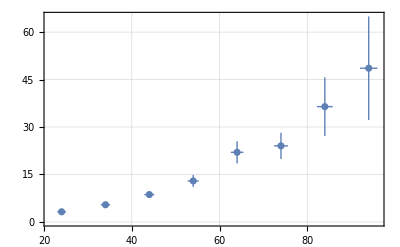

```mathematica
ListPlot[dataerr2,Frame->True,FrameStyle->Black,GridLines->Automatic,LabelStyle->{NumberPoint->","},BaseStyle->{FontFamily->"CMU Serif"},(*PlotLegends->MaTeX@functions,*)FrameLabel->MaTeX@{"\\text{Температура }t,\\ ^\\circ \\text{C}","\\text{Удельная проводимость }\\sigma_{\\text{пп}},\\ \\nicefrac{1}{\\text{Ом}\\cdot\\text{м}}"}]
```

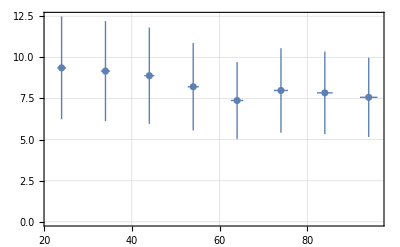

```mathematica
ListPlot[dataerr3,Frame->True,FrameStyle->Black,GridLines->Automatic,LabelStyle->{NumberPoint->","},BaseStyle->{FontFamily->"CMU Serif"},(*PlotLegends->MaTeX@functions,*)FrameLabel->MaTeX@{"\\text{Температура }t,\\ ^\\circ \\text{C}","\\text{Удельная проводимость }\\sigma_{\\text{пр}},\\ \\nicefrac{1}{\\text{мкОм}\\cdot\\text{м}}"}]
```

FittedModel[9.89078-0.0269792 x]

9.90.4

-0.0270.006

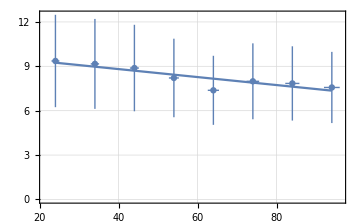

```mathematica
data=Table[{dataset1[n,"t"]["Value"],10^-3 dataset1[n,"spr"]["Value"]},{n,8}];
dataerr=dataerr3;
fit=LinearModelFit[data,{1,x},x](*   f = a + b * x   *)
fit["ParameterTable"];
a=Around[fit["BestFitParameters"]⟦1⟧,fit["ParameterErrors"]⟦1⟧]
b=Around[fit["BestFitParameters"]⟦2⟧,fit["ParameterErrors"]⟦2⟧]
(*fit["BestFitParameters"]⟦1⟧
fit["BestFitParameters"]⟦2⟧*)
(*hiTeXForm[a]
hiTeXForm[b]*)
Show[ListPlot[dataerr,Frame->True,FrameStyle->{Black,FontSize->12},ImageSize->Medium,GridLines->Automatic,LabelStyle->{NumberPoint->",",FontSize->12},BaseStyle->{FontFamily->"CMU Serif",FontSize->12},(*PlotLegends->MaTeX@functions,*)FrameLabel->MaTeX@{"\\text{Температура }t,\\ ^\\circ \\text{C}","\\text{Удельная проводимость }\\sigma_{\\text{пр}},\\ \\nicefrac{1}{\\text{мкОм}\\cdot\\text{м}}"}],Plot[fit["BestFitParameters"]⟦1⟧+fit["BestFitParameters"]⟦2⟧x,{x,Min[data⟦All,1⟧],Max[data⟦All,1⟧]}]]
```

```mathematica
data
```

{{24.,9.36},{34.,9.16295},{44.,8.88245},{54.,8.21208},{64.,7.37695},{74.,7.98606},{84.,7.84216},{94.,7.56939}}

```mathematica
Around[(9.36+7.57)/2,(9.36-7.57)/2]
```

8.50.9

```mathematica
(-0.0270.006)/(-8.31.0)
```

0.00330.0008

```mathematica
Mean[dataerr3]
```

{59.00.5,8.31.0}